```mathematica
dat=ReadList["V0=0.3-w=0.75.dat"];
datSolitons=Import["BS.txt","Table"];
zeroMode=Import["zero-mode-V0=0.3.dat","Table"];
extremalHBH = ReadList["extremal-V0=0.3.dat"];
```

```mathematica
V=0.3;
```

```mathematica
lenZM=Length[zeroMode];
rhZM=zeroMode[[All,-3]];
aZM=zeroMode[[All,-2]];
wZM=aZM/(aZM*aZM+rhZM*rhZM);
QeZM=V*(aZM*aZM+rhZM*rhZM)/rhZM;
MZM=(aZM*aZM+rhZM*rhZM+QeZM*QeZM)/(2*rhZM);
JZM=aZM*MZM;
```

```mathematica
extremalKN[x_]:=Sqrt[((1.0-4.0*V*V+Sqrt[(1.0+8.0*V*V)])/x)]/(2.0*Sqrt[(2.0*x)])
```

```mathematica
lenExtremal=Length[extremalHBH];
extremalw=extremalHBH[[All,1]];
extremalMass=extremalHBH[[All,3]];
extremalMH=extremalHBH[[All,4]];
extremalJ=extremalHBH[[All,5]];
extremalJH=extremalHBH[[All,6]];
extremalg=extremalHBH[[All,14]];
extremalQeINF=extremalHBH[[All,11]];
```

```mathematica
w=dat[[All,1]];
V0=dat[[All,2]];
Mass=dat[[All,3]];
MH=dat[[All,4]];
J=dat[[All,5]];
JH=dat[[All,6]];
Mint=-dat[[All,7]];
MintM=dat[[All,8]];
Mints=dat[[All,9]];
Jint=dat[[All,10]];
JintM=dat[[All,11]];
Jints=dat[[All,12]];
TH=dat[[All,13]];
AH=dat[[All,14]];
QeINF=dat[[All,15]];
muINF=dat[[All,16]];
rh=dat[[All,17]];
g=dat[[All,18]];
```

```mathematica
wSolitons = datSolitons[[All,1]];
MSolitons = datSolitons[[All,2]];
JSolitons = datSolitons[[All,3]];
```

```mathematica
len=Length[dat];
lenSolitons=Length[datSolitons];
```

```mathematica
solitonwM=ListPlot[Table[{wSolitons[[i]],MSolitons[[i]]},{i,1,lenSolitons}],PlotStyle->  Red,Joined->True];
zeroModePlot = ListPlot[Table[{wZM[[i]],MZM[[i]]},{i,1,lenZM}],PlotStyle->{Blue,Dashed},Joined->True];
extremalKNPlot = Plot[extremalKN[x],{x,0,1},PlotStyle->Black];
extremalHBHplot = ListPlot[Table[{extremalw[[i]],extremalMass[[i]]},{i,1,lenExtremal}],PlotStyle->Green,Joined->True];
```

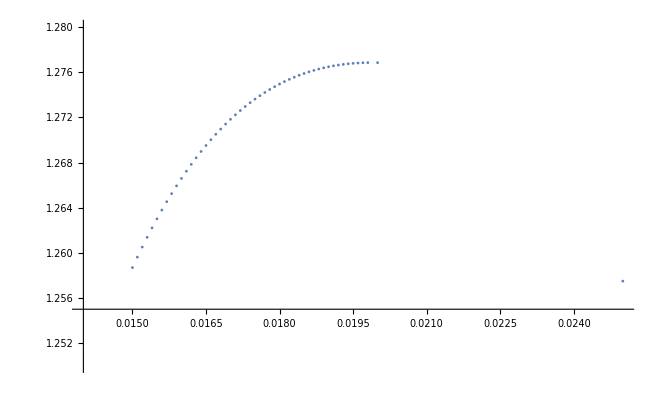

```mathematica
m=ListPlot[Table[{rh[[i]],Mass[[i]]},{i,1,len}],PlotStyle->PointSize[0.003]];
Show[m,PlotRange->{{0.014,0.025},{1.25,1.28}},AxesOrigin->{0.014,1.255}]
```